```mathematica
translate=Function[s,{s[[1]]+s[[2]],s[[2]]}];
leftColision=Function[s,If[
s[[1,1]]>=0,
s,
{s[[1]]*{-1,1},s[[2]]*{-1,1}}]
];
flipH=Function[s,
{
{1,0}-s[[1]],
{-1,1}*s[[2]]
}
];
flipD=s↦{{s[[1,2]],s[[1,1]]},{s[[2,2]],s[[2,1]]}};
rightColision=flipH@*leftColision@*flipH;
bottomColision=flipD@*leftColision@*flipD;
topColision=flipD@*rightColision@*flipD;
wallColision=Composition[leftColision,rightColision,bottomColision,topColision];
update=Composition[wallColision,translate];
```

```mathematica
state={{0.5,0.7},{0.01,-0.01}}
rate=1/60.;
Dynamic[ListPlot[{state[[1]]},PlotRange->{{0,1},{0,1}},AspectRatio->1,Frame->True]]
Dynamic[state]
While[True,state=update[state];Pause[rate]];
```

Function[{θ,θdot},{θdot,-Sin[θ]}]

{{0,1},{-Cos[θ],0}}

(0 | 1
-1 | 0)

(0 | 1
1 | 0)

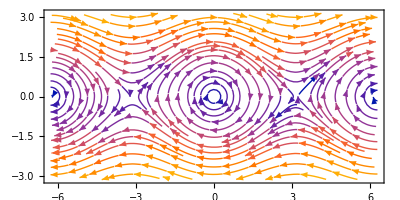

```mathematica
f={θ,θdot}↦{θdot,-Sin[θ]}
Grad[f[θ,θdot],{θ,θdot}]
%/.{θ->0}//MatrixForm
%%/.{θ->π}//MatrixForm
vp=StreamPlot[f[θ,θdot],{θ,-2π,2π},{θdot,-π,π},AspectRatio->1/2,StreamPoints->Fine]
```

```mathematica
eulerForward={f,h}↦s↦s+h Apply[f,s];
wrap=x↦Mod[x+2π,4π]-2π;
```

```mathematica
rk4={f,h}↦s↦Module[{f0,f1,f2,f3},
f0=Apply[f,s]; (* t = t0*)
f1=Apply[f,s+f0 h/2]; (* t = t0 + h/2 *)
f2=Apply[f,s+f1 h/2]; (* t = t0 + h/2 *)
f3=Apply[f,s+f2 h]; (* t = t0 + h *)
s+h/6(f0+2f1+2f2+f3)
];
```

```mathematica
update=rk4[f,0.02];
state={0,1};
```

```mathematica
fps=60.*10;
Dynamic@ListPlot[{{0,0},{Sin[state[[1]]],-Cos[state[[1]]]}},Joined->True,PlotRange->{{-1.1,1.1},{-1.1,1.1}},AspectRatio->1,Epilog->{PointSize[Large],Red,Point[{Sin[state[[1]]],-Cos[state[[1]]]}]}]
Dynamic@Show[vp,Epilog->{PointSize[Large],Red,Point[{wrap[state[[1]]],state[[2]]}]}]
Dynamic@state
While[True,state=update[state];Pause[1/fps]];
```

```mathematica
f0((x-(x0+δ/2))(x-(x0+δ)))/((x0-(x0+δ/2))(x0-(x0+δ)))+f1((x-x0)(x-(x0+δ)))/(((x0+δ/2)-x0)((x0+δ/2)-(x0+δ)))+f2((x-x0)(x-(x0+δ/2)))/(((x0+δ)-x0)((x0+δ)-(x0+δ/2)))
%//FullSimplify
%/.{{x->x0},{x->x0+δ/2},{x->x0+δ}}//Simplify
Integrate[%%,{x,x0,x0+δ}]
```

-(4 f1 (x-x0) (x-x0-δ))/δ^2+(2 f2 (x-x0) (x-x0-δ/2))/δ^2+(2 f0 (x-x0-δ) (x-x0-δ/2))/δ^2

f0+(2 (f0-2 f1+f2) (x-x0)^2)/δ^2-((3 f0-4 f1+f2) (x-x0))/δ

{f0,f1,f2}

(f0 δ)/6+(2 f1 δ)/3+(f2 δ)/6

```mathematica
update=eulerForward[f,0.02]
state={π/4.,0.}
update[state]
```

Function[s$,s$+0.02 Function[{θ,θdot},{θdot,-Sin[θ]}]@@s$]

{0.785398,0.}

{0.785398,-0.0141421}

```mathematica
update=rk4[f,0.02];
state={π/4.,0.}
update[state]
```

{0.785398,0.}

{0.785257,-0.0141415}